```mathematica
Data=Import["Import_data_8.xlsx"];
Data=Flatten[Data,1];
```

```mathematica
Data;
n=101;
k=10;
```

```mathematica
X=Standardize[Data];
A=Covariance[X];
Ev=Eigenvalues[A]
Table[Sum[Ev[[i]]/k,{i,1,j}],{j,1,k}]
```

{2.83148,1.70363,1.39519,1.15715,1.06065,0.928388,0.507567,0.207131,0.168325,0.0404927}

{0.283148,0.45351,0.593029,0.708745,0.81481,0.907648,0.958405,0.979118,0.995951,1.}

```mathematica
m=4;
Evec=Eigenvectors[A];
B=Table[Evec[[i]],{i,1,m}];
F=X.Transpose[B];
TableForm[F[[1;;5]]]
```

-0.52223 | -0.86173 | 1.31514 | 0.012532
1.83129 | 0.124335 | 0.201591 | 0.104158
-0.91934 | -1.85496 | -2.5314 | -0.071598
1.92878 | 0.000866521 | 0.584886 | 0.275099
1.91169 | -1.17214 | 0.015388 | 0.380584

```mathematica
Needs["HierarchicalClustering`"]
Needs["ANOVA`"]
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

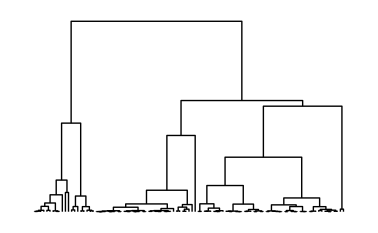

```mathematica
NCL=Range[1,n];
F0=MapThread[#1->#2&,{F,NCL}];
AC=Agglomerate[F0,Linkage->"Ward",DistanceFunction->SquaredEuclideanDistance];
DendrogramPlot[AC]
```

```mathematica
GroupN=14;
Groups=ClusterSplit[AC,GroupN];
Groups1=Table[ClusterFlatten[Groups[[i]]],{i,1,GroupN}]/.ClusterFlatten[x_]->{x}
```

{{1,68,16,42,40,78,8,83,46},{48},{101},{70},{29,77,49},{34,58,71,92,59},{2,25,36,99,4,60,17,80,81,9,10,15,22,72,76,67,87,13,91,35,39,50,95,86,38,20},{5,6,75,23,28,90},{18},{3,45,7,55,56,100,53,82,61},{33,52,97,84,88,73,11,65,63,12,30,62,64},{98,85,37,51,57,94,44,47,89,66,93,14,19,43},{41,69,96,21,79,26,31,54,27,32},{24,74}}

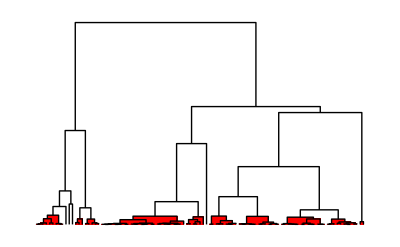

```mathematica
DendrogramPlot[AC,HighlightLevel->GroupN,HighlightStyle->Red]
```

```mathematica
FF=Table[Flatten[Table[Map[{i,#}&,F[[All,j]][[Groups1[[i]]]]],{i,1,GroupN}],1],{j,1,m}];
An=Table[ANOVA[FF[[i]],PostTests->Bonferroni,CellMeans->False],{i,1,m}]
```

{{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 250.334 | 19.2565 | 51.056 | 5.26872×10^-35
Error | 87 | 32.8133 | 0.377164 |  | 
Total | 100 | 283.148 |  |  | ,PostTests→{Model→Bonferroni | {{1,4},{2,4},{3,4},{1,5},{2,5},{1,6},{2,6},{4,6},{5,6},{1,7},{3,7},{4,7},{5,7},{6,7},{1,8},{3,8},{4,8},{5,8},{6,8},{4,9},{5,9},{6,9},{4,10},{5,10},{6,10},{7,10},{8,10},{4,11},{5,11},{6,11},{7,11},{8,11},{1,12},{3,12},{4,12},{5,12},{6,12},{7,12},{8,12},{10,12},{11,12},{1,13},{4,13},{5,13},{6,13},{7,13},{8,13},{3,14},{4,14},{5,14},{6,14},{8,14}}}},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 148.361 | 11.4124 | 45.1275 | 5.40694×10^-33
Error | 87 | 22.0016 | 0.252892 |  | 
Total | 100 | 170.363 |  |  | ,PostTests→{Model→Bonferroni | {{1,3},{2,3},{1,5},{3,5},{1,6},{3,6},{1,7},{3,7},{3,8},{5,8},{6,8},{7,8},{5,9},{6,9},{3,10},{5,10},{6,10},{7,10},{1,11},{3,11},{8,11},{10,11},{1,12},{3,12},{4,12},{7,12},{8,12},{9,12},{10,12},{11,12},{1,13},{2,13},{3,13},{4,13},{7,13},{8,13},{9,13},{10,13},{11,13},{12,13},{1,14},{2,14},{4,14},{5,14},{6,14},{7,14},{8,14},{9,14},{10,14},{11,14},{12,14},{13,14}}}},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 107.018 | 8.23213 | 22.036 | 3.82248×10^-22
Error | 87 | 32.5012 | 0.373577 |  | 
Total | 100 | 139.519 |  |  | ,PostTests→{Model→Bonferroni | {{1,3},{2,3},{1,5},{2,5},{3,5},{4,5},{1,6},{3,6},{1,7},{3,7},{5,7},{1,8},{3,8},{3,9},{1,10},{2,10},{3,10},{4,10},{7,10},{8,10},{1,11},{3,11},{10,11},{1,12},{3,12},{1,13},{3,13},{4,13},{7,13},{1,14},{2,14},{3,14},{4,14},{5,14},{6,14},{7,14},{8,14},{9,14},{10,14},{11,14},{12,14},{13,14}}}},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 99.8792 | 7.68301 | 42.2083 | 6.42166×10^-32
Error | 87 | 15.8363 | 0.182026 |  | 
Total | 100 | 115.715 |  |  | ,PostTests→{Model→Bonferroni | {{1,2},{2,3},{2,4},{1,5},{2,5},{4,5},{2,6},{5,6},{2,7},{5,7},{1,8},{2,8},{4,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{2,10},{5,10},{8,10},{9,10},{2,11},{5,11},{8,11},{9,11},{2,12},{5,12},{8,12},{9,12},{2,13},{5,13},{9,13},{10,13},{11,13},{12,13},{2,14},{5,14},{8,14},{9,14}}}}}

```mathematica
FF=Table[Flatten[Table[Map[{i,#}&,F[[All,j]][[Groups1[[i]]]]],{i,1,GroupN}],1],{j,1,m}];
An=Table[ANOVA[FF[[i]],PostTests ->Bonferroni,CellMeans->False],{i,1,m}]
GroupsTest={};
For[i=1,i≤m,i++,
v=An[[i,2,2,1,2,1,1,2]];
GroupsTest=Union[GroupsTest,v];
]
GroupsTest
Length[GroupsTest]==(GroupN(GroupN-1))/2
```

{{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 250.334 | 19.2565 | 51.056 | 5.26872×10^-35
Error | 87 | 32.8133 | 0.377164 |  | 
Total | 100 | 283.148 |  |  | ,PostTests→{Model→Bonferroni | {{1,4},{2,4},{3,4},{1,5},{2,5},{1,6},{2,6},{4,6},{5,6},{1,7},{3,7},{4,7},{5,7},{6,7},{1,8},{3,8},{4,8},{5,8},{6,8},{4,9},{5,9},{6,9},{4,10},{5,10},{6,10},{7,10},{8,10},{4,11},{5,11},{6,11},{7,11},{8,11},{1,12},{3,12},{4,12},{5,12},{6,12},{7,12},{8,12},{10,12},{11,12},{1,13},{4,13},{5,13},{6,13},{7,13},{8,13},{3,14},{4,14},{5,14},{6,14},{8,14}}}},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 148.361 | 11.4124 | 45.1275 | 5.40694×10^-33
Error | 87 | 22.0016 | 0.252892 |  | 
Total | 100 | 170.363 |  |  | ,PostTests→{Model→Bonferroni | {{1,3},{2,3},{1,5},{3,5},{1,6},{3,6},{1,7},{3,7},{3,8},{5,8},{6,8},{7,8},{5,9},{6,9},{3,10},{5,10},{6,10},{7,10},{1,11},{3,11},{8,11},{10,11},{1,12},{3,12},{4,12},{7,12},{8,12},{9,12},{10,12},{11,12},{1,13},{2,13},{3,13},{4,13},{7,13},{8,13},{9,13},{10,13},{11,13},{12,13},{1,14},{2,14},{4,14},{5,14},{6,14},{7,14},{8,14},{9,14},{10,14},{11,14},{12,14},{13,14}}}},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 107.018 | 8.23213 | 22.036 | 3.82248×10^-22
Error | 87 | 32.5012 | 0.373577 |  | 
Total | 100 | 139.519 |  |  | ,PostTests→{Model→Bonferroni | {{1,3},{2,3},{1,5},{2,5},{3,5},{4,5},{1,6},{3,6},{1,7},{3,7},{5,7},{1,8},{3,8},{3,9},{1,10},{2,10},{3,10},{4,10},{7,10},{8,10},{1,11},{3,11},{10,11},{1,12},{3,12},{1,13},{3,13},{4,13},{7,13},{1,14},{2,14},{3,14},{4,14},{5,14},{6,14},{7,14},{8,14},{9,14},{10,14},{11,14},{12,14},{13,14}}}},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 13 | 99.8792 | 7.68301 | 42.2083 | 6.42166×10^-32
Error | 87 | 15.8363 | 0.182026 |  | 
Total | 100 | 115.715 |  |  | ,PostTests→{Model→Bonferroni | {{1,2},{2,3},{2,4},{1,5},{2,5},{4,5},{2,6},{5,6},{2,7},{5,7},{1,8},{2,8},{4,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{2,10},{5,10},{8,10},{9,10},{2,11},{5,11},{8,11},{9,11},{2,12},{5,12},{8,12},{9,12},{2,13},{5,13},{9,13},{10,13},{11,13},{12,13},{2,14},{5,14},{8,14},{9,14}}}}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{9,10},{9,11},{9,12},{9,13},{9,14},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}

True

```mathematica
GroupN=14;
Groups=ClusterSplit[AC,GroupN];
Groups1=Table[ClusterFlatten[Groups[[i]]],{i,1,GroupN}]/.ClusterFlatten[x_]->{x}
FF=Table[Flatten[Table[Map[{i,#}&,F[[All,j]][[Groups1[[i]]]]],{i,1,GroupN}],1],{j,1,m}];
An=Table[ANOVA[FF[[i]],PostTests ->Bonferroni,CellMeans->False],{i,1,m}];
```

{{1,68,16,42,40,78,8,83,46},{48},{101},{70},{29,77,49},{34,58,71,92,59},{2,25,36,99,4,60,17,80,81,9,10,15,22,72,76,67,87,13,91,35,39,50,95,86,38,20},{5,6,75,23,28,90},{18},{3,45,7,55,56,100,53,82,61},{33,52,97,84,88,73,11,65,63,12,30,62,64},{98,85,37,51,57,94,44,47,89,66,93,14,19,43},{41,69,96,21,79,26,31,54,27,32},{24,74}}

```mathematica
CL=FindClusters[F0,GroupN,Method->"KMeans",DistanceFunction->SquaredEuclideanDistance]
```

{{1,11,12,30,35,39,42,50,62,68,86},{2,4,9,13,17,20,22,25,36,38,60,72,76,80,81,87,91,95,99},{3,7,45,56},{5,23,28,75,90},{6,53,55,61,82,100},{8,16,40,46,78,83},{10,14,15,19,32,37,43,51,57,66,67,85,89,93,94,96,98},{18},{21,26,27,31,41,44,47,54,69,79},{24,74},{29,34,49,70,71,77},{33,52,58,59,63,64,65,73,84,88,92,97},{48},{101}}

```mathematica
FVard=Table[F[[Groups1[[i]]]],{i,1,GroupN}];
ResSum=0;
For[i=1,i≤GroupN,i++,
clasterN=Length[Groups1[[i]]];
clasterMean=Mean[FVard[[i]]];
For[j=1,j≤clasterN,j++,
ResSum=ResSum+(Norm[FVard[[i,j]]-Mean[FVard[[i]]]]^2)/clasterN;
]];
ResSum
```

12.3939

```mathematica
Fkmeans=Table[F[[CL[[i]]]],{i,1,GroupN}];
ResSum=0;
For[i=1,i≤GroupN,i++,
clasterN=Length[CL[[i]]];
clasterMean=Mean[Fkmeans[[i]]];
For[j=1,j≤clasterN,j++,
ResSum=ResSum+(Norm[Fkmeans[[i,j]]-Mean[Fkmeans[[i]]]]^2)/clasterN;
]];
ResSum
```

14.8901